# GABE NOTEBOOK : Energy

Chris Shepherd, July 2020, christopher.shepherd-3@postgrad.manchester.ac.uk

Clear all variables to avoid naming conflicts.

```mathematica
ClearAll["Global`*"]
```

```mathematica
globalThickness=0.005;
globalFontSize=16;
globalFont="Latin Modern Mono Prop 10";
SetOptions[{ListPlot, ListLogPlot, Plot, LogPlot,ListLogLinearPlot,ListLogLogPlot,RegionPlot},LabelStyle->{ FontFamily->globalFont,FontSize-> globalFontSize, FontColor-> Black }, PlotStyle-> {Black, Thickness-> globalThickness}];
```

## PARAMETERS: Set parameters for where to read data and what to plot

```mathematica
dirlabel={"17445_64_1000_125", "17445_64_750"}; (*file name endings*)

numdirs=Length[dirlabel];
plotlabel="17445";
tAd=31;


dir=Table[{"C:\\Users\\admin\\Documents\\PhD_work\\R2HI\\Long paper\\GABE\\local_results_"<>dirlabel[[k]]<>"\\slices\\"},{k,1,numdirs}];(*directory to read from*)
```

## RUN DATA: Read in data and make plots for each run

```mathematica
intableE=Table[ReadList[dir[[k]]<>"slices_time.dat", Table[Real, {12}]] , {k,1,numdirs}];(*see g2output.cpp for ordering of output to slices_time"

tmaxFrac=.9
```

0.9

```mathematica
numtimes= Table[Round[tmaxFrac*(Length[intableE[[k]]]-1)] , {k,1,numdirs}]; (*cut one off becaues sometimes caught an error*)
```

```mathematica
etable=ConstantArray[0, {numdirs, 12}];
eFractable=ConstantArray[0, {numdirs, 12}];
eNtable=ConstantArray[0, {numdirs, 12}];
kIntable=ConstantArray[0,numdirs];
kInFracTable=ConstantArray[0,numdirs];
gInTable=ConstantArray[0,numdirs];
gInFracTable=ConstantArray[0,numdirs];
vInTable=ConstantArray[0,numdirs];
vInFracTable=ConstantArray[0,numdirs];
vInaTable=ConstantArray[0,numdirs];
vInFractable=ConstantArray[0,numdirs];
rhoIntable=ConstantArray[0,numdirs];
rhoInFractable=ConstantArray[0,numdirs];
kInaTable =ConstantArray[0,numdirs];
gInaTable =ConstantArray[0,numdirs];
vInaTable=ConstantArray[0,numdirs];
rhoInaTable=ConstantArray[0,numdirs];
totInaTable=ConstantArray[0,numdirs];
aTable=ConstantArray[0,numdirs];
For[k=1,k<numdirs+1 ,k++,
For[j=1, j<13, j++,
etable[[k,j]]=Table[{intableE⟦k,i,1⟧,intableE⟦k,i,j⟧},{i,1,numtimes[[k]]}];
eFractable[[k,j]]=Table[{intableE⟦k,i,1⟧,intableE⟦k,i,j⟧/intableE[[k,i,5]]},{i,1,numtimes[[k]]}];
]; (*2 kinetic, 3 potential, 4 gradient*)
eNtable[[k,5]]=Table[{intableE⟦k,i,1⟧,Log[intableE⟦k,i,5⟧/etable[[k,5,1,2]]]},{i,1,numtimes[[k]]}]; (* for N_e*)
kIntable [[k]]= Table[{intableE⟦k,i,1⟧, (intableE⟦k,i,2⟧-intableE⟦k,i,6⟧)}, {i,1,numtimes[[k]]}];
kInFracTable[[k]] =  Union[Table[{   intableE⟦k,i,1⟧, (intableE⟦k,i,2⟧-intableE⟦k,i,6⟧)/intableE⟦k,i,5⟧   }, {i,1,numtimes[[k]]}]];

gInTable[[k]] =  Union[Table[{   intableE⟦k,i,1⟧, intableE[[k,i,4]]   }, {i,1,numtimes[[k]]}]];
gInFracTable[[k]] =  Union[Table[{   intableE⟦k,i,1⟧, intableE[[k,i,4]]/intableE⟦k,i,5⟧   }, {i,1,numtimes[[k]]}]];
vInTable[[k]] = Union[Table[{intableE⟦k,i,1⟧, If[(intableE⟦k,i,3⟧-intableE⟦k,i,7⟧)>0, (intableE⟦k,i,3⟧-intableE⟦k,i,7⟧), (intableE⟦k,i,3⟧-intableE⟦k,i,7⟧)]}, {i,1,numtimes[[k]]}]];
vInFractable [[k]]= Union[Table[{intableE⟦k,i,1⟧, If[(intableE⟦k,i,3⟧-intableE⟦k,i,7⟧)>0, (intableE⟦k,i,3⟧-intableE⟦k,i,7⟧)/intableE[[k,i,5]], (*(intableE⟦i,3⟧-intableE⟦i,7⟧)/intableE[[i,5]]*)0.00000000000000000000000001/i]}, {i,1,numtimes[[k]]}]];
rhoIntable[[k]]=
Union[Table[{intableE⟦k,i,1⟧, kIntable[[k,i,2]]+gInTable[[k,i,2]]+vInTable[[k,i,2]],0}, {i,1,numtimes[[k]]}]];

rhoInFractable[[k]]=
Union[Table[{intableE⟦k,i,1⟧, kInFracTable[[k,i,2]]+gInFracTable[[k,i,2]]+vInFractable[[k,i,2]]}, {i,1,numtimes[[k]]}]];

aTable[[k]] =Table[{intableE⟦k,i,1⟧,intableE[[k,i,10]] },{i,1,numtimes[[k]]}];

kInaTable [[k]]=Table[{Log[aTable[[k,i]][[2]]],kInFracTable[[k,i]][[2]]}, {i,1,numtimes[[k]]}];
gInaTable [[k]]=Table[{Log[aTable[[k,i]][[2]]],gInFracTable[[k,i]][[2]]}, {i,1,numtimes[[k]]}];
vInaTable[[k]]=Table[{Log[aTable[[k,i]][[2]]],vInFractable[[k,i]][[2]]}, {i,1,numtimes[[k]]}];
rhoInaTable[[k]]= Table[{Log[aTable[[k,i]][[2]]],rhoInFractable[[k,i]][[2]]}, {i,1,numtimes[[k]]}];
totInaTable[[k]]= Table[{Log[aTable[[k,i]][[2]]],eFractable[[k,5]][[i]][[2]]}, {i,1,numtimes[[k]]}];
]
```

Plots of one directory

```mathematica
fracvst=ListLogPlot[{kInFracTable[[1]],gInFracTable[[1]],vInFractable[[1]],rhoInFractable[[1]], eFractable[[1,5]]}, Joined->True, PlotRange->{Automatic,{.001, 1}},PlotLegends->Placed[LineLegend[{"K_in", "G_in","V_in","ρ_in"}],{0.5,0}], AxesLabel->{"m_st", "Energy fraction"},
 PlotStyle->{Blue, Red, Green,Orange, Black}
]
```

-Graphics-

```mathematica
(*SetDirectory["C:\\Users\\admin\\Desktop\\paper\\figures"];
Export["fracvst_"<>plotlabel<>".pdf", fracvst]*)
```

SetDirectory::cdir: Cannot set current directory to C:\Users\admin\Desktop\paper\figures.

fracvst_17445.pdf

```mathematica
Show[ListPlot[Union[aTable[[1]]], Joined->True, PlotLabel->"scale factor with time",AxesLabel->{"program time", "a(t)"}, PlotLegends->{ "Exact scale factor"} ]];
```

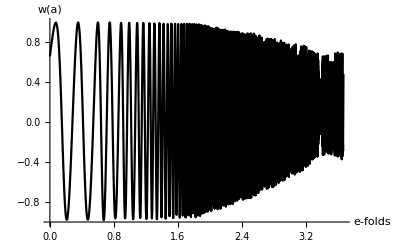

```mathematica
HvsA=Interpolation[Union[Table[{ Log[aTable[[1,i]][[2]]],Log[(etable[[1,5]][[i]][[2]])/3]}, {i,1,numtimes[[1]]}]]];
HvsAplot=Plot[-1-1/3HvsA'[a], {a,0, Log[aTable[[1,numtimes[[1]]]][[2]]]}, AxesLabel->{"e-folds", "w(a)"}, PlotStyle->Black, PlotRange->Automatic, AxesOrigin->{0,-1},
	GridLines->{None, {{0,Red}, {1/3,Red}}},
	GridLinesStyle->Automatic,
	Method-> {"GridLinesInFront"-> True}
	]
```

```mathematica
Export["wplot_"<>plotlabel<>".pdf", HvsAplot]
```

wplot_17445.pdf

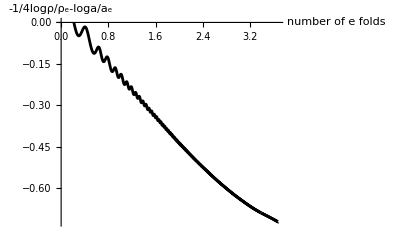

```mathematica
eNatable = Union[Table[{Log[aTable[[1,i]][[2]]], -1/4*eNtable[[1,5]][[i]][[2]]-Log[aTable[[1,i]][[2]]]}, {i,1, numtimes[[1]]}]];
ListPlot[eNatable, Joined-> True, AxesLabel->{"number of e folds", "-1/4logρ/ρ_e-loga/a_e"}]
```

```mathematica
fracvsa=ListLogPlot[{kInaTable[[1]],gInaTable[[1]],vInaTable[[1]],rhoInaTable[[1]], totInaTable[[1]]}, Joined->True, PlotRange->{0.01,1},PlotLegends->Placed[LineLegend[{"K_in", "G_in","V_in","ρ_in"}],{0.5,0}], AxesLabel->{"e folds", "Energy fraction"},
 PlotStyle->{Blue, Red, Green,Orange, Black}] (*plot against e-folds*)
(*SetDirectory["C:\\Users\\admin\\Desktop\\paper\\figures"];*)
```

SetDirectory::cdir: Cannot set current directory to C:\Users\admin\Desktop\paper\figures.

```mathematica
geff=106.75;
ms=N[Sqrt[1/(3*2*10^9)]];
Mp=2.44*10^18; (*reduced planck mass in GeV*);
tempTable = Table[{etable[[1,5]][[i,1]], (30/(Pi^2*geff)*etable[[1,5]][[i,2]])^(1/4)*ms^(1/2)*Mp}, {i,1,numtimes[[1]]}];
ListLogPlot[tempTable, Joined-> True];
```

Deriving formula for Ne

```mathematica
Mp=2.44*10^18;
Vs=1/(4*2*10^9)*Mp^4;
Ve=(1-Sqrt[3/4])^2*Vs;
g0=43/11;
gs=106.75;
1/3*Log[Pi^2/(30*Sqrt[27])]+Log[10^28]-1/3*Log[g0]+Log[Vs^(1/2)/(Ve^(1/4)*Mp)]-1/3*Log[Ve^(1/4)/10^13]
```

56.5027

```mathematica
N[Log[10^28]-1/4*Log[270/(Pi^2*g0^(4/3))]-1/12*Log[gs]-1/4*Log[Ve/Vs]-1/4*Log[Mp^4/Vs]]
```

59.0147

```mathematica
%-1/12*Log[Ve/10^(13*4)]+1/12*Log[Pi*gs/30]
```

57.3162

Plot with ticks

```mathematica
tfun=InverseFunction[Interpolation[aTable[[1]]]]; (*tpr as function of a*)
```

```mathematica
nwidth=.5;
nmax=Round[Max[Table[Log[aTable[[1,i,2]]], {i,1,Length[aTable[[1]]]}]],nwidth]
```

3.5

```mathematica
ticks1=Table[nwidth*i, {i,0,nmax/nwidth}];
ticks2=Table[Round[tfun[Exp[ticks1[[i]]]]] , {i,1, Length[ticks1]}];
ticks2tab=Table[{ticks1[[i]], ticks2[[i]]}, {i,2,Length[ticks1]}];
ticks0tab =Table[{ticks1[[i]], " "}, {i,2,Length[ticks1]}];
ticksy = Table[10^-i, {i,0,100}];
```

```mathematica
aFun=Interpolation[aTable[[1]]];
```

```mathematica
Log[aFun[tAd]]
```

1.37305

```mathematica
evsaPlot=
Show[
ListLogPlot[{kInaTable[[1]],gInaTable[[1]],vInaTable[[1]],rhoInaTable[[1]], totInaTable[[1]]}, Joined->True, PlotRange->{All,{0.0025,1.7}},PlotLegends->Placed[LineLegend[{"K_in", "G_in","V_in","ρ_in"}],{0.5,0}], AxesLabel->{"e-folds", "Energy fraction"},
 PlotStyle->{Blue, Red, Green,Orange, {Black, Thickness-> .0001}} ,Ticks-> {ticks1, Automatic}(*,
	Epilog-> {
			Style[Text[ ticks2[[2]],{ticks1[[2]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[3]],{ticks1[[3]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[4]],{ticks1[[4]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[5]],{ticks1[[5]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[6]],{ticks1[[6]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[7]],{ticks1[[7]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[8]],{ticks1[[8]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			(*Style[Text[ ticks2[[9]],{ticks1[[9]],Log[1.6]}   ],FontFamily->Times,18],
			Style[Text[ ticks2[[10]],{ticks1[[10]],Log[1.6]}   ],FontFamily->Times,18],*)


			Style[Text["|",{ticks1[[2]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[3]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[4]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[5]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[6]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[7]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[8]],Log[1.07]}   ],FontFamily-> globalFont,8],
			(*Style[Text["|",{ticks1[[9]],Log[1.07]}   ],FontFamily->Times,6],
			Style[Text["|",{ticks1[[10]],Log[1.07]}   ],FontFamily->Times,6],*)
			
			Style[Text["m_st",{4,Log[1.0]}   ],FontFamily->globalFont,globalFontSize]
		}*)
,PlotRangeClipping->False,
GridLines-> { {{Log[aFun[tAd]],Black} }, None},
GridLinesStyle->Dashed
],
Epilog-> {
			Style[Text[ ticks2[[2]],{ticks1[[2]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[3]],{ticks1[[3]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[4]],{ticks1[[4]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[5]],{ticks1[[5]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[6]],{ticks1[[6]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[7]],{ticks1[[7]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			Style[Text[ ticks2[[8]],{ticks1[[8]],Log[1.6]}   ],FontFamily-> globalFont,globalFontSize],
			(*Style[Text[ ticks2[[9]],{ticks1[[9]],Log[1.6]}   ],FontFamily->Times,18],
			Style[Text[ ticks2[[10]],{ticks1[[10]],Log[1.6]}   ],FontFamily->Times,18],*)


			Style[Text["|",{ticks1[[2]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[3]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[4]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[5]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[6]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[7]],Log[1.07]}   ],FontFamily-> globalFont,8],
			Style[Text["|",{ticks1[[8]],Log[1.07]}   ],FontFamily-> globalFont,8],
			(*Style[Text["|",{ticks1[[9]],Log[1.07]}   ],FontFamily->Times,6],
			Style[Text["|",{ticks1[[10]],Log[1.07]}   ],FontFamily->Times,6],*)
			
			Style[Text["m_ϕ^(+)t",{4,Log[1.0]}   ],FontFamily->globalFont,globalFontSize]
		}
]
```

-Graphics-

```mathematica
Export["evsa_"<>plotlabel<>".pdf", evsaPlot]
```

evsa_17445.pdf

Late time scale factor

```mathematica
rhoStart=etable[[1,5]][[1]][[2]];
rhoIn0=rhoIntable[[1,numtimes[[1]]]][[2]];
rhoHom0=etable[[1,5]][[numtimes[[1]]]][[2]]-rhoIn0;
tStop=aTable[[1,numtimes[[1]]]][[1]];
```

```mathematica
b=2*10^9;
tGamma=ms*144*Sqrt[6]*Pi^2*b^(3/2);

aLate=NDSolveValue[{a'[t]/a[t]==(1/3*((rhoHom0*aFun[tStop]^3)/a[t]^3+(rhoIn0*aFun[tStop]^4)/a[t]^4))^(1/2), a[tStop]==aFun[tStop]}, a, {t,tStop, tGamma}];
rhoLate[t_]:=(rhoHom0*aFun[tStop]^3)/aLate[t]^3+(rhoIn0*aFun[tStop]^4)/aLate[t]^4;
NeLate[t_]:=-1/4*Log[rhoLate[t]/rhoLate[tStop]]-Log[aLate[t]/aLate[tStop]]
```

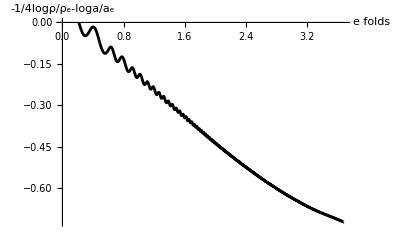

```mathematica
ListPlot[eNatable, Joined-> True, AxesLabel->{"e folds", "-1/4logρ/ρ_e-loga/a_e"}]
ParametricPlot[{ Log[aLate[t]],NeLate[t]}, {t,tStop,tGamma}, AspectRatio->1/2, PlotRange->All, AxesLabel->{"e folds", "-1/4logρ/ρ_d-loga/a_d"}];
```

Pure R^2 limit

```mathematica
aR=NDSolveValue[{a'[t]/a[t]==(1/3*rhoStart/a[t]^3)^(1/2), a[0]==1}, a, {t,0, tGamma}];
rhoR[t_]:=rhoStart/aR[t]^3;
NeR[t_]:=-1/4*Log[rhoR[t]/rhoR[0]]-Log[aR[t]/1]
```

Contribution to N_e after end of rescattering (after run-time)

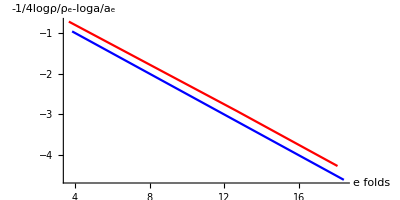

```mathematica
ListPlot[eNatable, Joined-> True, AxesLabel->{"e folds", "-1/4logρ/ρ_e-loga/a_e"}];
Show[{
ParametricPlot[{ Log[aLate[t]],NeLate[t]+eNatable[[Length[eNatable],2]](*eNatable[[numtimes,2]][[1]]*)}, {t,tStop,tGamma},PlotStyle->Red],
ParametricPlot[{ Log[aR[t]],NeR[t]}, {t,tStop,tGamma},PlotStyle->Blue]
}, AspectRatio-> 1/2,AxesLabel->{"e folds", "-1/4logρ/ρ_e-loga/a_e "} ,PlotRange-> All, AxesOrigin-> {0,0}]
(*N[59-54.37]*) (*nice, agrees with the blue line*)
```

```mathematica
eNatable[[Length[eNatable],2]];
```

-0.722703

```mathematica
ListPlot[{aTable[[1]], Table[{etable[[1,5]][[i]][[1]],(1+3/2*Sqrt[1/3*etable[[1,5]][[1]][[2]]]*etable[[1,5]][[i]][[1]])^(2/3)}, {i,1,numtimes[[1]]}],
			Table[{etable[[1,5]][[i]][[1]],(1+2*Sqrt[1/3*etable[[1,5]][[1]][[2]]]*etable[[1,5]][[i]][[1]])^(1/2)}, {i,1,numtimes[[1]]}]}, Joined-> True,PlotStyle->{Black, Blue, Green}, PlotLegends->{"results", "MD", "RD"}];
```

Comparing different directories

```mathematica
rhovsPlotTable=Table[ListLogPlot[
{rhoInaTable[[k]],totInaTable[[k]]},
 Joined->True, PlotRange->{.001,1},PlotLegends->Placed[LineLegend[{"ρ_in ("<>ToString[k]<>")" }],{0.5,0}], AxesLabel->{"e folds", "Energy fraction"},
 PlotStyle->{Hue[k/numdirs], Black}]
, {k,1,numdirs}];
```

```mathematica
rhovsaAll=Show[rhovsPlotTable]
```

-Graphics-

Late-time scalaron decay

```mathematica
b=1.7445*10^9;
xi1=Sqrt[(2*10^9 -b)*l];
```

```mathematica
ms=Sqrt[1/(3*(xi1^2+l*b))];
```

```mathematica
intablemass=ReadList[dir[[1]]<>"mass_vs_time.dat", Table[Real,{2}]]; (*square masses*)
numtimesmass = Length[intablemass]-1;

	masstable=Union[Table[{intablemass⟦i,1⟧,intablemass⟦i,2⟧},{i,1,numtimesmass}]];
```

```mathematica
msq0=masstable[[numtimesmass, 2]];
```

```mathematica
t0Run=tStop;
dtRun=tStop;
dtRunC=tStop;
```

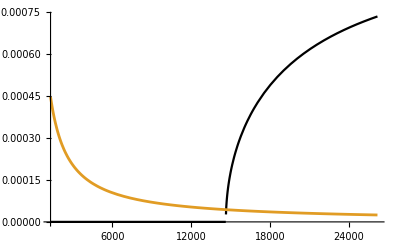

```mathematica
gamPhi[t_]:= If[(2msq0*aLate[tStop]^2)/aLate[t]^2<1, Re[4/(24*Pi^2)*xi1^2/(ms^2 b^2)*Sqrt[1-(2msq0*aLate[tStop]^2)/aLate[t]^2]], 0];  (*if kinematically allowed, can efficiently decay once Gamma_phi larger than Hubble*)
(*check if kinematically possible for phi to decay into two higgses*)
Plot[{gamPhi[t], Sqrt[1/3 * rhoLate[t]]}, {t,tStop,20tStop}] (*once black>yellow, can decay*)
```